```mathematica
SetDirectory["~/star/git/v1_CGF2015/images"]
```

/Volumes/playpen/narain/star/git/v1_CGF2015/images

```mathematica
point[u_,v_]:=u{1,0}+v{1/2,Sqrt@3/2};
points=Flatten[Table[point[u,v],{u,-5,10},{v,0,10}],1];
dirs=Table[{Cos@t,Sin@t},{t,0,2π/3,π/3}];
lines=Flatten[Table[{p,p+d},{p,points},{d,dirs}],1];
```

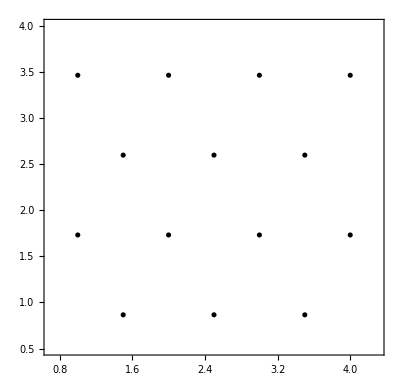

```mathematica
ListPlot[points,PlotRange->{{0.7,4.3},{0.5,4}},AspectRatio->Automatic,PlotStyle->Black,Axes->None,Frame->True]
```

```mathematica
mesh[points_]:=MeshPrimitives[DelaunayMesh[points],1]
```

```mathematica
vertices[points_,points2_]:={PointSize[0.03],Black,Point/@points,RGBColor[0.9,0.2,0.2],Point/@points2}
```

```mathematica
thick=Thick;
thin=Thickness[Medium];
```

```mathematica
pr={{1.35,4.65},{0.7,2.8}};
```

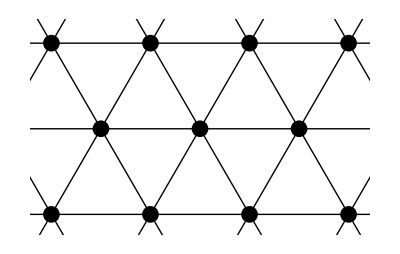

```mathematica
Graphics[{thick,mesh[points],vertices[points,{}]},PlotRange->pr]
```

```mathematica
Export["remeshing-base.pdf",%];
```

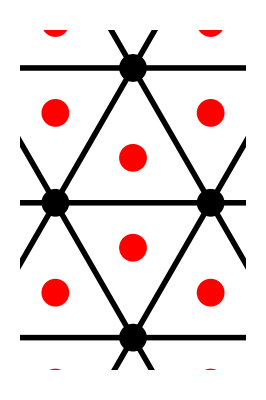

```mathematica
dirs2=Table[1/Sqrt@3{Cos@t,Sin@t},{t,π/6,5π/6,π/3}];
points2=Mean@*First/@MeshPrimitives[DelaunayMesh[points],2];
Graphics[{thick,mesh[points],vertices[points,points2]},PlotRange->pr]
```

```mathematica
Export["remeshing-sqrt3-1.pdf",%];
```

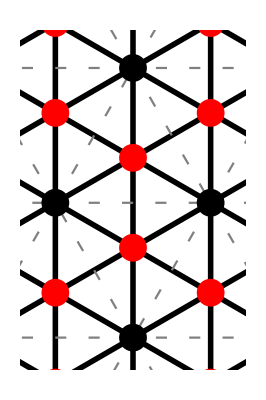

```mathematica
Graphics[{thick,mesh[points~Join~points2],Gray,Dashing[{0.02,0.04}],thin,mesh[points],vertices[points,points2]},PlotRange->pr]
```

```mathematica
Export["remeshing-sqrt3-2.pdf",%];
```

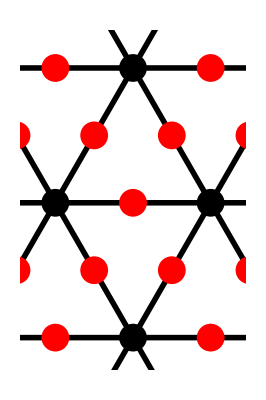

```mathematica
points4=Mean@*First/@MeshPrimitives[DelaunayMesh[points],1];
Graphics[{thick,mesh[points],vertices[points,points4]},PlotRange->pr]
```

```mathematica
Export["remeshing-bisect-1.pdf",%];
```

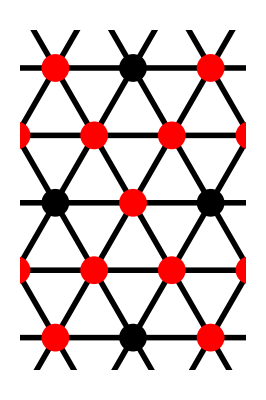

```mathematica
Graphics[{thick,mesh[points~Join~points4],vertices[points,points4]},PlotRange->pr]
```

```mathematica
Export["remeshing-bisect-2.pdf",%];
```

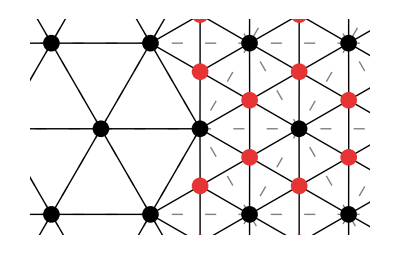

```mathematica
points2b=#+{0.001,0}&/@Select[points2,First@#>2.75&];
Graphics[{{Gray,Dashing[{0.02,0.04}],thin,mesh[points]},thick,mesh[points~Join~points2b],vertices[points,points2b]},PlotRange->pr]
```

```mathematica
Export["remeshing-sqrt3.pdf",%];
```

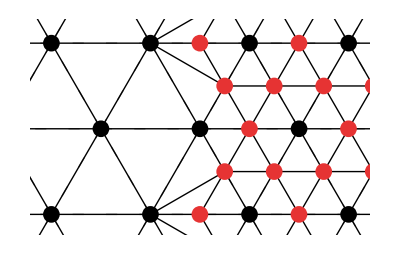

```mathematica
points4b=#-{0.001,0}&/@Select[points4,First@#>2.75&];
Graphics[{{Gray,Dashing[{0.02,0.04}],thin,mesh[points]},thick,mesh[points~Join~points4b],vertices[points,points4b]},PlotRange->pr]
```

```mathematica
Export["remeshing-bisect.pdf",%];
```

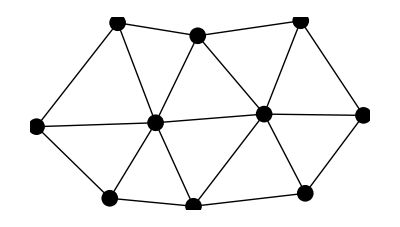

```mathematica
SeedRandom[2];
{pa,pb,pc,pi,pj,pk,pl,pu,pv,pw}=0.1RandomVariate[NormalDistribution[],2]+#&/@{point[0,0],point[1,0],point[2,0],point[-1,1],point[0,1],point[1,1],point[2,1],point[-1,2],point[0,2],point[1,2]};
Graphics[{vertices[{pa,pb,pc,pi,pj,pk,pl,pu,pv,pw},{}],thick,Line/@{{pa,pb},{pb,pc},{pi,pj},{pj,pk},{pk,pl},{pu,pv},{pv,pw},{pa,pi},{pa,pj},{pb,pj},{pb,pk},{pc,pk},{pc,pl},{pi,pu},{pj,pu},{pj,pv},{pk,pv},{pk,pw},{pl,pw}}}]
```

```mathematica
Export["remeshing-local-base.pdf",%];
```

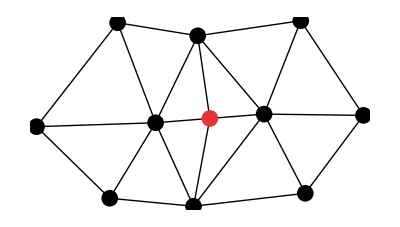

```mathematica
Graphics[{thick,Line/@{{pa,pb},{pb,pc},{pi,pj},{pj,pk},{pk,pl},{pu,pv},{pv,pw},{pa,pi},{pa,pj},{pb,pj},{pb,pk},{pc,pk},{pc,pl},{pi,pu},{pj,pu},{pj,pv},{pk,pv},{pk,pw},{pl,pw},{pb,(pj+pk)/2},{pv,(pj+pk)/2}},vertices[{pa,pb,pc,pi,pj,pk,pl,pu,pv,pw},{(pj+pk)/2}]}]
```

```mathematica
Export["remeshing-local-split.pdf",%];
```

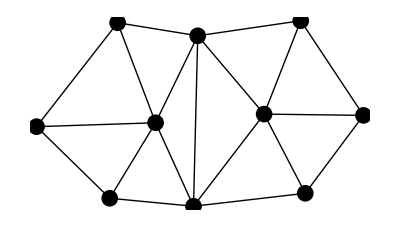

```mathematica
Graphics[{thick,Line/@{{pa,pb},{pb,pc},{pi,pj},{pb,pv},{pk,pl},{pu,pv},{pv,pw},{pa,pi},{pa,pj},{pb,pj},{pb,pk},{pc,pk},{pc,pl},{pi,pu},{pj,pu},{pj,pv},{pk,pv},{pk,pw},{pl,pw}},vertices[{pa,pb,pc,pi,pj,pk,pl,pu,pv,pw},{}]}]
```

```mathematica
Export["remeshing-local-flip.pdf",%];
```

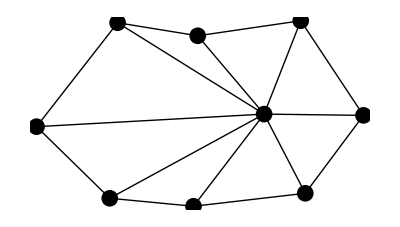

```mathematica
Graphics[{thick,Line/@{{pa,pb},{pb,pc},{pi,pk},{pk,pl},{pu,pv},{pv,pw},{pa,pi},{pa,pk},{pb,pk},{pc,pk},{pc,pl},{pi,pu},{pk,pu},{pk,pv},{pk,pw},{pl,pw}},vertices[{pa,pb,pc,pi,pk,pl,pu,pv,pw},{}]}]
```

```mathematica
Export["remeshing-local-collapse.pdf",%];
```

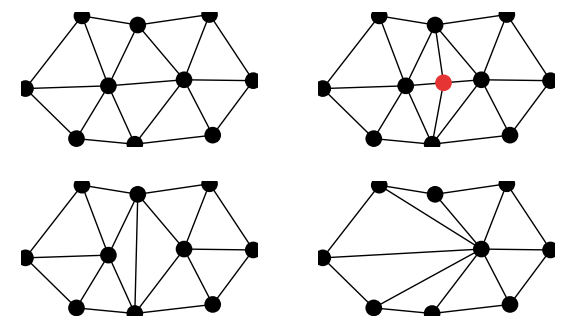

```mathematica
GraphicsGrid[{{%%%%,%%%},{%%,%}},ImageSize->Large]
```

```mathematica
Export["remeshing-local.pdf",%];
```